```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];

(*!!!const*) colvar={2,3,4};(* Number of columns that are used as intital data*) 
(* Model with 1 var - 1st element of the set. The added var. - the 2nd element of the set. Result - the 3rd elem*)

(*!!!const*) multifl=1; (*1 -fitting multivar model*)

(*!!!const*) {xs,ys}={200,200};
(*!!!const*) {xs2,ys2}={400,350};

pathlist={SystemDialogInput["FileOpen",".xlsx"]};
pathlist=Flatten[pathlist,1];
If[pathlist=={$Canceled},Exit[]];
namein=pathlist[[1]];
RawDat=Import[namein][[1]];

(*------------Calculatin F-test-------------*)
Ftest[resf_,ress_,n_,p_,d_]:=Module[{Fstat=0}, (*gives identical result as anova table*)
Fstat=((ress-resf)/d)/(resf/(n-p-1));
1-N[CDF[FRatioDistribution[d,(n-p-1)],Fstat]]
]
(*------------------------------------------*)
```

FittedModel[-1.60215+0.955998 x]

AnovA table | DF | SS | MS | F-Statistic | P-Value
x | 1 | 49.447 | 49.447 | 49.3639 | 9.90076×10^-10
Error | 72 | 72.1212 | 1.00168 |  | 
Total | 73 | 121.568 |  |  |

RSS 72.1212

BestFitParameters intercept+ Log_VL_Rx = Setpoint {-1.60215,0.955998}

Parameter CI {{-3.34135,0.13705},{0.684754,1.22724}}

ParameterPValues {0.07043,9.90076×10^-10}

AdjustedRSquared 0.398503

RSquared 0.406743

number of points 74

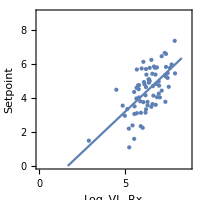

FittedModel[-1.79056+0.918892 x1+0.00602631 x2]

AnovA table | DF | SS | MS | F-Statistic | P-Value
x1 | 1 | 49.447 | 49.447 | 60.6943 | 4.08628×10^-11
x2 | 1 | 14.2783 | 14.2783 | 17.526 | 0.000080102
Error | 71 | 57.843 | 0.81469 |  | 
Total | 73 | 121.568 |  |  |

RSS 57.843

BestFitParameters  intercept + Log_VL_Rx + Day_of_Rx  = Setpoint {-1.79056,0.918892,0.00602631}

Parameter CI {{-3.36199,-0.219135},{0.673577,1.16421},{0.00315604,0.00889658}}

ParameterPValues {0.0261179,1.60976×10^-10,0.000080102}

AdjustedRSquared 0.51079

RSquared 0.524193

number of points 74

F-test 0.000080102

-Graphics3D-

```mathematica
(********************************************************************************************)
colres=Length[colvar];(*creating initial table based on variables*)

m1col=colvar[[{1,colres}]];
varname=RawDat[[1,m1col]]; 
FitDat=Rest[RawDat[[All,m1col]]];
FitDat=Cases[FitDat,{_?NumberQ,_?NumberQ}];

Model1=LinearModelFit[FitDat,x,x];
Print[Model1];
Print["AnovA table",AT1=Model1["ANOVATable"]];
Resid=Model1["FitResiduals"];
Print["RSS ",RSS1=Sum[Resid[[i]]^2,{i,1,Length[Resid]}]];
Print["BestFitParameters ","intercept+ ",varname[[1]]," = ",varname[[2]]," ",Bfp=Model1["BestFitParameters"]];
Print["Parameter CI ",PCI=Model1["ParameterConfidenceIntervals"]];
Print["ParameterPValues ",Bfpp=Model1["ParameterPValues"]];
Print["AdjustedRSquared ",Model1["AdjustedRSquared"]];
Print["RSquared ",Model1["RSquared"]];
Print["number of points ",Length[FitDat]];

{minx,maxx}={0,1.05*Max[FitDat[[All,1]]]};
Print[grout =Show[Plot[Model1[x],{x,0,maxx},PlotRange->{{0,1.05*maxx},{0,9}},AspectRatio->1,Frame->True,FrameLabel->{varname[[1]],varname[[2]]},LabelStyle->{Blue,Bold,FontSize->12},ImageSize->{xs,ys}],ListPlot[FitDat,PlotStyle->PointSize[Medium]]]];


(***********************)
If[multifl==1,

m2col=colvar[[{1,2,colres}]];
varname2=RawDat[[1,m2col]]; 
FitDat=Rest[RawDat[[All,m2col]]];
FitDat=Cases[FitDat,{_?NumberQ,_?NumberQ,_?NumberQ}];
Model2=LinearModelFit[FitDat,{x1,x2},{x1,x2},IncludeConstantBasis->True];
Print[Model2];
Print["AnovA table",AT2=Model2["ANOVATable"]];
Resid=Model2["FitResiduals"];
Print["RSS ",RSS2=Sum[Resid[[i]]^2,{i,1,Length[Resid]}]];
Print["BestFitParameters "," intercept + ",varname2[[1]]," + ",varname2[[2]]," = ",varname2[[3]]," ",Bfp2=Model2["BestFitParameters"]];
Print["Parameter CI ",PCI2=Model2["ParameterConfidenceIntervals"]];
Print["ParameterPValues ",Bfpp2=Model2["ParameterPValues"]];
Print["AdjustedRSquared ",Model2["AdjustedRSquared"]];
Print["RSquared ",Model2["RSquared"]];
Print["number of points ",Length[FitDat]];
Print["F-test ",ft=Ftest[RSS2,RSS1,Length[FitDat],2,1]];(*number of predictors not naber of parameters! number of predictors=number of parameters-1*)



{minx,maxx}={0,1.05*Max[FitDat[[All,1]]]};
{miny, maxy}={0,1.05*Max[FitDat[[All,2]]]};
{minz, maxz}={0,1.05*Max[FitDat[[All,3]]]};

ptgr=ListPointPlot3D[FitDat,PlotStyle->Directive[Black,PointSize[Large]],AxesLabel->{varname2[[1]],varname2[[2]],varname2[[3]]},ImageSize->{xs2,ys2},LabelStyle->{Blue,Bold,FontSize->12},AxesStyle->Thick,PlotRange->{{minx,maxx},{miny, maxy},{0,7}} ,AspectRatio->7/9];
fngr1=Plot3D[Model2[xx,yy],{xx,minx,maxx},{yy,miny, maxy},AxesLabel->{varname2[[1]],varname2[[2]],varname2[[3]]},ImageSize->{xs2,ys2},LabelStyle->{Blue,Bold,FontSize->12},AxesStyle->Thick,PlotRange->{{minx,maxx},{miny, maxy},{minz, maxz}} ,AspectRatio->7/9,PlotStyle->Directive[Opacity[0.6],Orange],PlotPoints->50,MaxRecursion->15,PerformanceGoal->"Quality",WorkingPrecision->8];
Print[grout=Show[fngr1,ptgr]];
]

(********************)
```